## Functions

```mathematica
Clear[Dominates];
Dominates[p_,q_,m_]:=Block[{},
pans=#[p]&/@m;
qans=#[q]&/@m;
And@@{Or@@(#⟦1⟧<#⟦2⟧&/@Transpose[{pans,qans}]),
And@@(#⟦1⟧≤#⟦2⟧&/@Transpose[{pans,qans}])}
]
```

```mathematica
FastNonDominatedSort[Pin_,m_]:=Block[{},
F[1]={};
Map[Block[{},
p=#;
Map[Block[{},
q=#;
n[p]=0;
If[Dominates[p,q,m],
AppendTo[S[p],q],
If[Dominates[q,p,m],
n[p]=n[p]+1;
]
]]&,Pin];
If[n[p]==0,
AppendTo[F[1],p]
];
]&,Pin];
i=1;
While[Length[F[i]]>0,
H={};
Map[Block[{p=#},
Map[Block[{q=#},
n[q]=n[q]-1;
If[n[q]==0,
AppendTo[H,q]];
]&,S[p]]
]&,F[i]];
i++;
F[i]=H;
];
F[#]&/@Range[i-1]
]
```

```mathematica
CrowdingDistanceAssignment[Iin_,m_]:=Module[{Idistance,Isorted,l,I,Iorder},
I=Iin;
l=Length[I];
Set[Idistance[#],0]&/@Range[l];
Map[Block[{n=#},
Iorder=Ordering[I,All,n[#1]<n[#2]&];
Idistance[0]=Idistance[l]=∞;
Map[Block[{i=#},
Idistance[i]=Idistance[i]+(n[I⟦Iorder⟦i+1⟧⟧]-n[I⟦Iorder⟦i-1⟧⟧]);
]&,Range[2,l-1]];
]&,m];
Idistance[#]&/@Range[l]
]
```

```mathematica
DominationRank[P_List,m_List]:=Block[{},
Map[Block[{p=#},
P2=Map[Block[{q=#},
Dominates[p,q,m]
]&,P];
Count[P2,False]
]&,P]
]
```

```mathematica
CrowdedComparisonOperator[i_List,j_List]:=Block[{},
(i⟦3⟧<j⟦3⟧)||((i⟦3⟧==j⟦3⟧)&&(i⟦2⟧>j⟦2⟧))
]
```

#### Random Numbers

```mathematica
RandomUnion[no_]:=Block[{randlist=Range[no],rand,randno},Table[rand=RandomInteger[{1,Length[randlist]}];randno=randlist⟦rand⟧;randlist=Drop[randlist,{rand}];randno,{no}]]
```

```mathematica
RandomUnion[no_,subno_]:=Block[{randlist=Range[no],rand,randno},Table[rand=RandomInteger[{1,Length[randlist]}];randno=randlist⟦rand⟧;randlist=Drop[randlist,{rand}];randno,{subno}]]
```

```mathematica
randomnumbers[number_]:=(SeedRandom[];RandomReal[{0,1},number])
```

```mathematica
bin6[b_,c_]:=b[[#]]&/@Split[Ordering[c],c[[#1]]==c[[#2]]&];
```

#### SelectforCrossover

```mathematica
Clear[SelectforCrossover]
```

```mathematica
SelectforCrossover[list_,pc_:0.25,m_]:=Block[{rnos,numbers,breeding={}},
numbers=Length[list];
While[Length[breeding]<numbers,
rnos=RandomInteger[{1,numbers},{4}];
dom=DominationRank[#,m]&/@list⟦rnos⟧;
AppendTo[breeding,rnos⟦Position[dom,Min[dom]]⟦1,1⟧⟧];
];
breeding]
```

#### Crossover

```mathematica
outsiderange[value_,start_,end_]:=Which[(2start-value)>end,end,(2end-value)<start,start,value<start,outsiderange[2start-value,start,end],value>end,outsiderange[2end-value,start,end],value≥start&&value≤end,value]
```

```mathematica
crossovermethods={"Biased","Interpolated","SBX"}
```

{Biased,Interpolated,SBX}

```mathematica
InvDistC[x_,n_]:=Switch[Random[Integer,{0,1}],0,1^(1/(1+n)) x^(1/(1+n)),1,Abs[ 2^(-1/(1+n))(0.5-1 x)^(-1/(1+n))]]
```

```mathematica
CrossoverSBX[datalistin_,crosslist_,start_,end_]:=Block[{datalist=datalistin,lengths,crossingpositions,randomcrossingpositions,pairedcrossingpositions,crosseddata},
crossingpositions=crosslist;
randomcrossingpositions=RandomUnion[Length[crossingpositions]];
pairedcrossingpositions=Partition[crossingpositions⟦randomcrossingpositions⟧,2];
crosseddata=Block[{chrom=datalistin⟦#⟧},SBX[chrom]]&/@pairedcrossingpositions;
((datalist=ReplacePart[datalist,#⟦1⟧->#⟦2⟧])&/@#)&/@MapThread[Transpose[{##}]&,{pairedcrossingpositions,crosseddata}];CheckRange[datalist,start,end]]
```

```mathematica
SBX[inputin_]:=Block[{absmeans,relmeans,orders,a,input=Sort[inputin]},
absmeans=Mean[#]&/@Transpose[input];
relmeans=Mean[#-Min[#]]&/@Transpose[input];
orders=Ordering[#]&/@Transpose[input];
betas=InvDistC[Random[Real,{0,1}],$betafactor];
a=Switch[Random[Integer,{0,1}],1,{#⟦1⟧-(#⟦2⟧*betas),#⟦1⟧+(#⟦2⟧*betas)},0,#⟦4⟧]&/@Transpose[{absmeans,relmeans,orders,Transpose[input]}];
Transpose[a]
]
```

```mathematica
CheckRange[data_,start_,end_]:=
outsiderange[Sequence@@#]&/@Transpose[{#,If[ListQ[start],start,Table[start,{Length[#]}]],If[ListQ[end],end,Table[end,{Length[#]}]]}]&/@data
```

```mathematica
CrossoverBiased[datalistin_,crosslist_,start_,end_]:=Block[{datalist=datalistin,lengths,crossingpositions,randomcrossingpositions,pairedcrossingpositions,crosseddata},
crossingpositions=Select[crosslist,#⟦2⟧===True&]⟦All,1⟧;
randomcrossingpositions=RandomUnion[Length[crossingpositions]];
pairedcrossingpositions=Partition[crossingpositions⟦randomcrossingpositions⟧,2];
(*Print[pairedcrossingpositions];*)
crosseddata=Transpose[Module[{chrom=datalistin⟦#⟧},If[RandomReal[{0,1}]<$parentbias,#,Reverse[#]]&/@Transpose[chrom]]]&/@pairedcrossingpositions;
(*Print[MapThread[Transpose[{##}]&,{pairedcrossingpositions,crosseddata}]];*)
((datalist=ReplacePart[datalist,#⟦1⟧->#⟦2⟧])&/@#)&/@MapThread[Transpose[{##}]&,{pairedcrossingpositions,crosseddata}];datalist]
```

```mathematica
CrossoverInterpolated[datalistin_,crosslist_,start_,end_]:=Block[{datalist=datalistin,lengths,crossingpositions,randomcrossingpositions,pairedcrossingpositions,crosseddata,p},
crossingpositions=Select[crosslist,#⟦2⟧===True&]⟦All,1⟧;
randomcrossingpositions=RandomUnion[Length[crossingpositions]];
pairedcrossingpositions=Partition[crossingpositions⟦randomcrossingpositions⟧,2];
(*Print[pairedcrossingpositions];*)
crosseddata=Transpose[Module[{chrom=datalistin⟦#⟧},{#⟦1⟧(p=RandomReal[{-1,1}])+(1-p)#⟦2⟧,#⟦2⟧(p=RandomReal[{-1,1}])+(1-p)#⟦1⟧}&/@Transpose[chrom]]]&/@pairedcrossingpositions;

((datalist=ReplacePart[datalist,#⟦1⟧->#⟦2⟧])&/@#)&/@MapThread[Transpose[{##}]&,{pairedcrossingpositions,crosseddata}];CheckRange[datalist,start,end]]
```

#### Mutate

```mathematica
mutationmethods={"Gaussian","Scaled"}
```

{Gaussian,Scaled}

```mathematica
MutateGaussian[value_,start_,end_,mutationsize_]:=outsiderange[value+Random[NormalDistribution[0,mutationsize]],start,end]
```

```mathematica
MutateScaled[value_,start_,end_,mutationsize_]:=outsiderange[value*RandomReal[{-mutationsize,mutationsize}],start,end]
```

```mathematica
Mutate[list_,mr_,start_,end_,mutationmethod_,mutationsize_]:=Block[{},
Module[{data=Transpose[{#,If[ListQ[start],start,Table[start,{Length[#]}]],If[ListQ[end],end,Table[end,{Length[#]}]],If[ListQ[mutationsize],mutationsize,Table[mutationsize,{Length[#]}]]}]},
If[RandomReal[{0,1}]<mr,mutationmethod[Sequence@@##],#⟦1⟧]&/@data]&/@list
]
```

```mathematica
GetIterationNumber[]:=iterationno
```

## MOP4

```mathematica
Clear[f1,f2]
```

```mathematica
f1[x_List]:=f1[x]=Sum[(-10Exp[-0.2(x⟦i⟧^2+x⟦i+1⟧^2)^0.5]),{i,1,2}]
```

```mathematica
f2[x_List]:=f2[x]=Sum[Abs[x⟦i⟧]^0.8+5 Sin[x⟦i⟧]^3,{i,1,3}]
```

```mathematica
nochroms=10;
ranges={-5,5};
functions={f1,f2};
pop1=RandomReal[ranges,{nochroms,10}];
pop2=RandomReal[ranges,{nochroms,10}];
Generations={pop1,pop2};
SelectedGenerations={};
Do[
PopCombined=Join[Generations⟦-2⟧,Generations⟦-1⟧];
PopFNDS=FastNonDominatedSort[PopCombined,functions];
PopSelected=Block[{PopNew,crowd,dom},
PopNew={};
If[Length[Flatten[PopNew,1]]<nochroms,
PopNew=Join[PopNew,{#}];
If[Length[Flatten[PopNew,1]]≥nochroms,
crowd=CrowdingDistanceAssignment[Last[PopNew],functions];
dom=DominationRank[Last[PopNew],functions];
sortingdata=Transpose[{Last[PopNew],crowd,dom}];
sorteddata=Sort[sortingdata,CrowdedComparisonOperator];
finaldata=Join[Most[PopNew],{Take[sorteddata,nochroms-Length[Flatten[Most[PopNew],1]]]⟦All,1⟧}]
];
]&/@PopFNDS;
Flatten[finaldata,1]
];
AppendTo[SelectedGenerations,mutatedpop];
breeding=SelectforCrossover[PopSelected,0.5,functions];
$betafactor=1;
crossedpop=CrossoverSBX[PopSelected,breeding,Sequence@@ranges];
mutatedpop=Mutate[crossedpop,0.2,Sequence@@ranges,MutateScaled,1];
AppendTo[Generations,mutatedpop];
,{200}]
```

$Aborted

```mathematica
Dynamic[If[Length[SelectedGenerations]>10,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦-10;;-1⟧,PlotRange->All,PlotRange->{{-20,-14},{-12,0}},Frame->True,PlotStyle->(GrayLevel[1-#/5]&/@Range[5])]]]
```

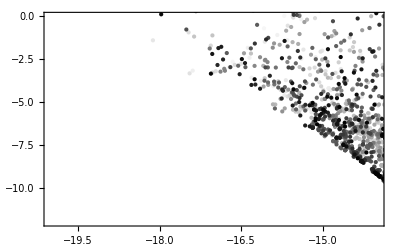

```mathematica
ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦All⟧,
PlotRange->{{-20,-14},{-12,0}},Frame->True,PlotStyle->(GrayLevel[1-#/Length[Generations]]&/@Range[Length[SelectedGenerations]])]
```

## EC6

```mathematica
Clear[f1,f2,g]
```

```mathematica
f1[x_List]/;(Length[x]===10):=f1[x]=(1-Exp[-4 x⟦1⟧] Sin[6π x⟦1⟧]^6)
```

f2[x_List]/;(Length[x]===10)&&Head[x⟦1⟧]===Real:=(g[x](1-(f1[x]/g[x])^2))

g[x_List/;(Length[x]===10)]:=(1+9(Total[Rest[x]]/9)^0.25)

```mathematica
f2[x_List]/;(Length[x]===10):=f2[x]=((1+9(Total[Rest[x]]/9)^0.25)(1-(f1[x]/(1+9(Total[Rest[x]]/9)^0.25))^2))
```

```mathematica
SelectedGenerations={}
```

{}

f1ans = Block[{a, b, c, d, e, f, g, h, i, j},
  NMinimize[{f1[{a, b, c, d, e, f, g, h, i, j}], 0 <= a <= 1, 0 <= b <= 1, 0 <= c <= 1, 0 <= d <= 1, 0 <= e <= 1, 0 <= f <= 1, 0 <= g <= 1, 0 <= h <= 1, 0 <= i <= 1, 0 <= j <= 1}, {{a, 0, 1}, {b, 0, 1}, {c, 0, 1}, {d, 0, 1}, {e, 0, 1}, {f, 0, 1}, {g, 0, 1}, {h, 0, 1}, {i, 0, 1}, {j, 0, 1}}]
  ]

{0.280775,{a→0.0814578,b→0.260294,c→0.593644,d→0.874568,e→0.421055,f→0.512892,g→0.53817,h→0.546698,3→0.801226,j→0.422492}}

f2ans = Block[{a, b, c, d, e, f, g, h, i, j},
  NMinimize[{f2[{a, b, c, d, e, f, g, h, i, j}], 0 <= a <= 1, 0 <= b <= 1, 0 <= c <= 1, 0 <= d <= 1, 0 <= e <= 1, 0 <= f <= 1, 0 <= g <= 1, 0 <= h <= 1, 0 <= i <= 1, 0 <= j <= 1}, {{a, 0, 1}, {b, 0, 1}, {c, 0, 1}, {d, 0, 1}, {e, 0, 1}, {f, 0, 1}, {g, 0, 1}, {h, 0, 1}, {i, 0, 1}, {j, 0, 1}}, Method -> "DifferentialEvolution", MaxIterations -> 60]
  ]

```mathematica
nochroms=20;
ranges={0,1};
functions={f1,f2};
pop1=RandomReal[ranges,{nochroms,10}];
pop2=RandomReal[ranges,{nochroms,10}];
Generations={pop1,pop2};
SelectedGenerations={};
Do[
PopCombined=Join[Generations⟦-2⟧,Generations⟦-1⟧];
PopFNDS=FastNonDominatedSort[PopCombined,functions];
PopSelected=Block[{PopNew,crowd,dom},
PopNew={};
If[Length[Flatten[PopNew,1]]<nochroms,
PopNew=Join[PopNew,{#}];
If[Length[Flatten[PopNew,1]]≥nochroms,
crowd=CrowdingDistanceAssignment[Last[PopNew],functions];
dom=DominationRank[Last[PopNew],functions];
sortingdata=Transpose[{Last[PopNew],crowd,dom}];
sorteddata=Sort[sortingdata,CrowdedComparisonOperator];
finaldata=Join[Most[PopNew],{Take[sorteddata,nochroms-Length[Flatten[Most[PopNew],1]]]⟦All,1⟧}]
];
]&/@PopFNDS;
Flatten[finaldata,1]
];
AppendTo[SelectedGenerations,mutatedpop];
breeding=SelectforCrossover[PopSelected,0.5,functions];
$betafactor=1;
crossedpop=CrossoverSBX[PopSelected,breeding,Sequence@@ranges];
mutatedpop=Mutate[crossedpop,0.2,Sequence@@ranges,MutateScaled,1];
AppendTo[Generations,mutatedpop];
,{200}]
```

Join::heads: Heads List and Mutate at positions 1 and 2 are expected to be the same.

If::argb: If called with 6 arguments; between 2 and 4 arguments are expected.

$Aborted

```mathematica
Dynamic[If[Length[SelectedGenerations]>10,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦-10;;-1⟧,PlotRange->All,Frame->True,PlotStyle->(GrayLevel[1-#/5]&/@Range[5])]]]
```

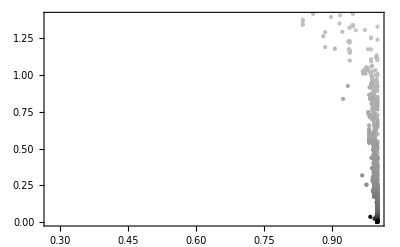

```mathematica
ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦All⟧,
PlotRange->{{0.28,1},{0,1.4}},Frame->True,PlotStyle->(GrayLevel[1-#/Length[Generations]]&/@Range[Length[SelectedGenerations]])]
```